## Possibly Useful Identities

Orthogonal:  If Qᵀ.Q=I then dQᵀQ+Qᵀ.dQ=0 and W=Qᵀ.dQ is skew since
	dQᵀQ=-Qᵀ.dQ

Projection:  If P.P=P then dP.P+P.dP=dP and 
	dP.P+P.dP-dP=0
or equivalently 
	dP.(P-I)+P.dP=0
which says with P̂=I-P 
	dP.P̂=P.dP
This one has lots of variants.

Orthogonal Projection:  If P=I-Q.Qᵀ then dP=-dQ.Qᵀ-Q.dQᵀ. Is there anything useful in the structure of the RHS? Well perhaps since
	dP.Q=-dQ.Qᵀ.Q-Q.dQᵀ.Q=-dQ+Q.Qᵀ.dQ=(I-P).dQ
Lots of ways to write this
	dP.Q=P̂.dQ=Q.Qᵀ.dQ=-Q.dQᵀ.Q
Not sure of this is helpful or not.

# Arnoldi AD Implementation

The first couple of sections are working out how to implement AD (1st and 2nd directional derivatives) as an after computation of the Arnoldi computation.

## Arnoldi Code and Test

Note, m is the size of A while n is the depth of the Arnoldi recursion.

```mathematica
Arnoldi[A_][b_,n_]:= Module[
{m=Length[A],Q,H,w,q},
Q=ConstantArray[0.0,{m,n+1}];
H=ConstantArray[0.0,{n+1,n}];
(* Assuming b is normalized! *)
Q⟦All,1⟧=b;
Do[
w=A.Q⟦All,j⟧;
Do[
H⟦k,j⟧=Q⟦All,k⟧.w;
w=w-H⟦k,j⟧ Q⟦All,k⟧,
{k,1,j}];
H⟦j+1,j⟧=Norm[w];
Q⟦All,j+1⟧=w/H⟦j+1,j⟧,
{j,1,n}
];
{Q,H}
]
```

```mathematica
m=300;
A=RandomReal[{-√(2/m),√(2/m)},{m,m}]; 
{i,j,k}={12,17,18};{γ,α,β}={1.3,0.2,0.3};
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
b=Normalize[RandomReal[{-1,1},m]];
n=10;
{Q,H}=Arnoldi[A][b,n];
TableForm[{
{UpperTriangularMatrixQ[H,-1],OrthogonalMatrixQ[Q]},
{Dimensions[Q]=={m,n+1},Dimensions[H]=={n+1,n}},
Map[Norm,{Qᵀ.Q-IdentityMatrix[n+1],A.Q⟦All,1;;n⟧-Q.H}],
{Min[Diagonal[H,-1]],H⟦n+1,n⟧}
},TableHeadings->{{"Structure","Dimensions","Residuals","Subdiagonal"},None}]
```

Structure | True | True
Dimensions | True | True
Residuals | 5.05544×10^-16 | 7.6058×10^-16
Subdiagonal | 0.760469 | 0.806137

## AD Initialization

I have v_0∈ℝ^n and W=[w_1 | | | w_2 | | | … | | | w_b]∈ℝ^(n×b) with Wᵀ.W=I_b and Wᵀ.v_0=0_b.  The easiest way to make such a thing is by partitioning the orthogonalization of a random n×(b+1)  matrix.  This makes the initialization simple.

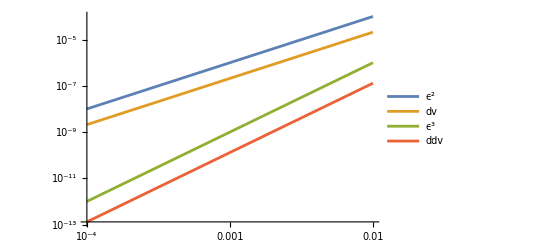

```mathematica
{n,b}={23,4};
vW=QRDecomposition[RandomReal[{-1,1},{n,b+1}]]⟦1⟧ᵀ;
v0=vW⟦All,1⟧; W=vW⟦All,2;;b+1⟧;
Map[Norm,{Wᵀ.W-IdentityMatrix[b],Wᵀ.v0,v0}];
v[ϵ_]:=(v0+W.ϵ)(1+ϵ.ϵ)^(-1/2)
dv[ϵ_,u1_]:= W.u1(1+ϵ.ϵ)^(-1/2)-(v0+W.ϵ)(1+ϵ.ϵ)^(-3/2)ϵ.u1
ddv[ϵ_,u1_,u2_]:=(3(v0+W.ϵ)(1+ϵ.ϵ)^(-5/2)(ϵ.u1 )(ϵ.u2)
-W.u1(1+ϵ.ϵ)^(-3/2)ϵ.u2 -W.u2(1+ϵ.ϵ)^(-3/2)ϵ.u1 -(v0+W.ϵ)(1+ϵ.ϵ)^(-3/2)u1.u2
)
(* Tangent line and quadratic approximation *)
(* scaling behavior single direction *)
x0=RandomReal[{-1,1},b];
{u1,u2}=Map[Normalize,RandomReal[{-1,1},{2,b}]];
LogLogPlot[{
ϵ^2,
Norm[v[x0+ϵ u1]-(v[x0]+ϵ dv[x0,u1])],
ϵ^3,
Norm[v[x0+ϵ u1]-(v[x0]+ϵ dv[x0,u1]+1/2 ϵ^2 ddv[x0,u1,u1])]
},
{ϵ,10^-4,10^-2},
PlotLegends->{"ϵ^2","dv","ϵ^3","ddv"}
]
```

Checking that I have first and second derivatives correct in the two direction sense.

```mathematica
g={dv[x0,u1],dv[x0,u2]};
H=({{ddv[x0,u1,u1], ddv[x0,u1,u2]}, {ddv[x0,u2,u1], ddv[x0,u2,u2]}});
{α1,α2}=RandomReal[{-1,1},2];
(* Tangent line and quadratic approximation *)
(* scaling behavior single direction *)
TabView[{
"lin"->ContourPlot[ 
Norm[
v[x0+ϵ1 u1+ ϵ2 u2]-(v[x0]+{ϵ1,ϵ2}.g)
],
{ϵ1,-0.01,0.01},{ϵ2,-0.01,0.01},
PlotLegends->Automatic,
Contours->20],
"quad"->ContourPlot[ 
Norm[
v[x0+ϵ1 u1+ ϵ2 u2]-(v[x0]+{ϵ1,ϵ2}.g+1/2{ϵ1,ϵ2}.({ϵ1,ϵ2}.H))
],
{ϵ1,-0.01,0.01},{ϵ2,-0.01,0.01},
PlotLegends->Automatic,
Contours->20],
"slice"->LogLogPlot[{
ϵ^2,
Norm[v[x0+ϵ (α1 u1+α2 u2)]-(v[x0]+ϵ {α1,α2}.g )],
ϵ^3,
Norm[v[x0+ϵ (α1 u1+α2 u2)]-(v[x0]+ϵ {α1,α2}.g+1/2 ϵ^2 {α1,α2}.({α1,α2}.H))]
},
{ϵ,10^-4,10^-2},
PlotLegends->{"ϵ^2","lin","ϵ^3","quad"}]
}]
```

123

The Arnoldi process (with no initial scaling) is being defined on the surface of the n-1 dimensional unit sphere 𝒮_(m-1)=∂ℬ_m⊂ℝ^m.  Provided Wᵀ.v_0=0 and Wᵀ.W=I_b the function v:ℬ_b→𝒮_(m-1)⊂ℝ^m defined by 
	v[ϵ]=(v_0+W.ϵ)(1+ϵ.ϵ)^(-1/2)
is a smooth parameterization of a b dimensional patch of 𝒮_(m-1).  The formula above give
	q_1(0) | = | v_0 |   |  
∂_j q_1(0) | = | W.e_j | = | w_j
∂_(j,k) q_1(0) | = | v_0(e_j.e_k) | = | δ_(j,k)v_0
These let us “start” AD computations for the Arnoldi process.

## AD Rewrite

```mathematica
ArnoldiAD[A_][v0_,n_,u1_,u2_]:= Module[
{m=Length[A],Q,dQ,ddQ,H,dH,ddH,w,dw,ddw,q,dq,ddq},
Q=dQ=ddQ=ConstantArray[0.0,{m,n+1}];
H=dH =ddH=ConstantArray[0.0,{n+1,n}];
(* Initializing derivatives of v[ϵ] from above  *)
(* Assuming v0 is normalized and W = [u1|u2] *)
(* satisfies Wᵀ.v0 = 0 and Wᵀ.W=Subscript[I, 2] *)
Q⟦All,1⟧=v0;dQ⟦All,1⟧=u1;ddQ⟦All,1⟧=-v0;(* ddQ⟦All,1⟧=-v0(u1.u2); PERTURBATION CONFUSION!! *)
(* Differentiating the code.  *)
Do[
w=A.Q⟦All,j⟧;dw=A.dQ⟦All,j⟧; ddw=A.ddQ⟦All,j⟧;
Do[
(* H and derivatives *)
H⟦k,j⟧=Q⟦All,k⟧.w;
dH⟦k,j⟧=dQ⟦All,k⟧.w+Q⟦All,k⟧.dw;  (*1st Der *)
ddH⟦k,j⟧=ddQ⟦All,k⟧.w+2dQ⟦All,k⟧.dw+Q⟦All,k⟧.ddw;  (* 2nd Der *)
(* w and derivatives. *)
ddw=ddw-ddH⟦k,j⟧ Q⟦All,k⟧-2dH⟦k,j⟧ dQ⟦All,k⟧-H⟦k,j⟧ ddQ⟦All,k⟧; (* 2nd Der *)
dw=dw-dH⟦k,j⟧ Q⟦All,k⟧-H⟦k,j⟧ dQ⟦All,k⟧; (* 1st Der *)
w=w-H⟦k,j⟧ Q⟦All,k⟧,
{k,1,j}];
(* Subdiagonal and Derivatives *)
H⟦j+1,j⟧=(w.w)^(1/2);
dH⟦j+1,j⟧=(w.w)^(-1/2)(w.dw); (* 1st Der *)
ddH⟦j+1,j⟧=-(w.w)^(-3/2)(w.dw)^2+(w.w)^(-1/2)(w.ddw+dw.dw);(* 2nd Der *)
(* Final Scaling and Derivatives *)
Q⟦All,j+1⟧=w H⟦j+1,j⟧^-1;
dQ⟦All,j+1⟧=dw H⟦j+1,j⟧^-1-w dH⟦j+1,j⟧H⟦j+1,j⟧^-2; (* 1st Der *)
ddQ⟦All,j+1⟧=ddw H⟦j+1,j⟧^-1 -2 dw dH⟦j+1,j⟧H⟦j+1,j⟧^-2+2 w H⟦j+1,j⟧^-3 dH⟦j+1,j⟧^2 -w H⟦j+1,j⟧^-2 ddH⟦j+1,j⟧  (* 2nd Der *)
,
{j,1,n}
];
{{Q,H},{dQ,dH},{ddQ,ddH}}
]
```

Testing

```mathematica
{m,b}={23,2};
A=RandomReal[{-1,1},{m,m}];
vW=QRDecomposition[RandomReal[{-1,1},{m,b+1}]]⟦1⟧ᵀ;v0=vW⟦All,1⟧; W=vW⟦All,2;;b+1⟧;
{u1,u2}=Wᵀ;zeros=ConstantArray[0.0,b];
n=4;{{Q,H},{dQ,dH},{ddQ,ddH}}=ArnoldiAD[A][v0,n,u1,u2];
Map[Norm,{A.Q⟦All,1;;n⟧-Q.H,A.dQ⟦All,1;;n⟧-dQ.H-Q.dH,A.ddQ⟦All,1;;n⟧-ddQ.H-2dQ.dH-Q.ddH}]
Map[Norm,{dQᵀ.Q+Qᵀ.dQ,ddQᵀ.Q+2dQᵀ.dQ+Qᵀ.ddQ}]
```

{8.94694×10^-16,8.47347×10^-16,1.22096×10^-15}

{7.00937×10^-16,2.39804×10^-15}

```mathematica
{MatrixPlot[Chop[Qᵀ.ddQ+ddQᵀ.Q+2dQᵀ.dQ],PlotLegends->Automatic]}
```

{-Graphics-}

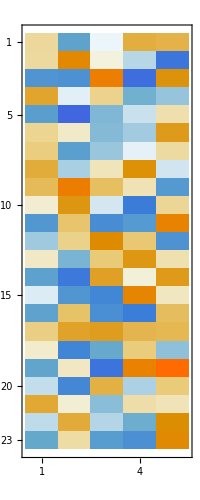

```mathematica
MatrixPlot[Chop[ddQ]]
```

```mathematica
f[{h1_,h2_}]:=v[{h1,h2}]
(* 1st Derivatives *)
Map[Norm,{u1-D[f[{h1,h2}],h1],u2-D[f[{h1,h2}],h2]}/.{h1->0,h2->0}]
D[f[{h1,h2}],h1,h1]/.{h1->0,h2->0}
D[f[{h1,h2}],h1,h2]/.{h1->0,h2->0}
D[f[{h1,h2}],h2,h1]/.{h1->0,h2->0}
D[f[{h1,h2}],h2,h2]/.{h1->0,h2->0}
v0
```

{0.,0.}

{0.114117,0.111406,-0.322739,0.32341,-0.262882,0.136748,0.173972,0.301541,0.243669,0.0446864,-0.307485,-0.134246,0.0591533,-0.254005,-0.0467526,-0.25215,0.170953,0.0549996,-0.238633,-0.0913697,0.31124,-0.0937792,-0.214193}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.114117,0.111406,-0.322739,0.32341,-0.262882,0.136748,0.173972,0.301541,0.243669,0.0446864,-0.307485,-0.134246,0.0591533,-0.254005,-0.0467526,-0.25215,0.170953,0.0549996,-0.238633,-0.0913697,0.31124,-0.0937792,-0.214193}

{-0.114117,-0.111406,0.322739,-0.32341,0.262882,-0.136748,-0.173972,-0.301541,-0.243669,-0.0446864,0.307485,0.134246,-0.0591533,0.254005,0.0467526,0.25215,-0.170953,-0.0549996,0.238633,0.0913697,-0.31124,0.0937792,0.214193}

```mathematica
?D
```